```mathematica
(*Outputs {escape time, estimate maximum error}*)
TEscape[b_,en_,ϕsh_]:=Module[{initVelocities,escTime,sol,enSquaredNumerical,error,maxError,t},
escTime=MaximumT+1;
initVelocities=getVelocities[b,en,ϕsh];
sol=Quiet@NDSolve[{ddrho[b],ddθ[b],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->25];
enSquaredNumerical[σ_]=(ρ'[σ]^2+ρ[σ](ρ[σ]-1)θ'[σ]^2+(1-1/ρ[σ])(1+((l[b]-b*ρ[σ]^2*Sin[θ[σ]]^2)^2)/(ρ[σ]^2 Sin[θ[σ]]^2)))/.First@sol;
error[σ_]=Abs[en^2-enSquaredNumerical[σ]];
maxError=First@NMaximize[{error[t],0≤t≤escTime},t,Method-> "DifferentialEvolution"];
Return[{escTime,maxError}]
];
```

```mathematica
iV=getVelocities[0.1,1.2,(565 π)/999]
```

{0.751338,0.156987}

```mathematica
sol=Quiet@NDSolve[{ddrho[0.1],ddθ[0.1],ρ[0]==3,ρ'[0]==iV⟦1⟧,θ[0]==π/2,θ'[0]==iV⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->25,MaxSteps->∞];//AbsoluteTiming
```

{39.3206,Null}

```mathematica
enSquaredNumerical[σ_]=(ρ'[σ]^2+ρ[σ](ρ[σ]-1)θ'[σ]^2+(1-1/ρ[σ])(1+((l[0.1]-0.1*ρ[σ]^2*Sin[θ[σ]]^2)^2)/(ρ[σ]^2 Sin[θ[σ]]^2)))/.First@sol;
```

```mathematica
error[σ_]=Abs[1.2^2-enSquaredNumerical[σ]];
```

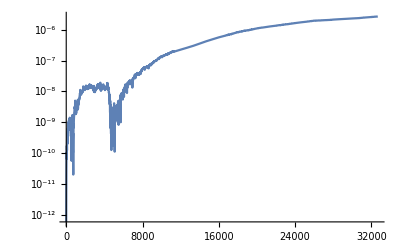

```mathematica
LogPlot[error[t],{t,0,escTime}]
```

```mathematica
error[escTime]
```

2.71407×10^-6

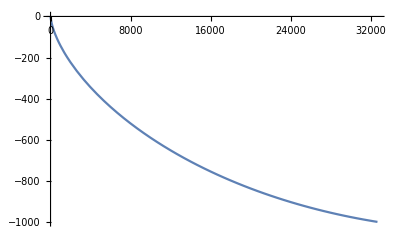

```mathematica
Plot[ρ[σ]Cos[θ[σ]]/.sol,{σ,0,escTime}]
```

```mathematica
escTime
```

32667.433881013687919

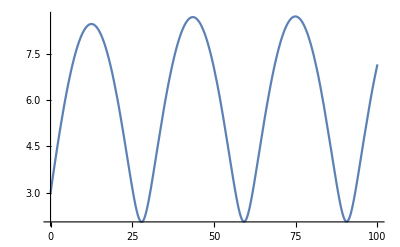

```mathematica
Plot[ρ[σ]Sin[θ[σ]]/.sol,{σ,0,100}]
```

```mathematica
escTime
```

32666.5757647776643065118345452

```mathematica
(565 π)/999//N
```

1.77678

```mathematica
π/2//N
```

1.5708

## Positive l

```mathematica
$IsPositive=True;
```

### ε=1.2

```mathematica
ε=1.2;
```

#### b=0.1

```mathematica
b=0.1;Progress=0;
(*rawData produces a (numTrajectories x 2) matrix with the 1st column being the set of different escape times, and the 2nd column being the set of different maximum errors*)
rawData=Monitor[ParallelTable[Progress++;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],Progress]; //AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45731.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{28.3942,Null}

```mathematica
rawData⟦;;,1⟧
```

{2168.721540227500279464916,1000001,1000001,1000001,286.3243688527190534573475,2038.352078750639969524874,2024.946760821315239074319,1650.895466300681920107808,1000001,1000001,3.409453852792002949417807,2.585682922217472937726502,2.318255485956742255799238,2.404136634311196929048724,2.891897280267060241577133,4.557783665141575717302467,1726.545831114092150031543,130.6336052129021933665931,34.26514186902305217099219,65.14899280196270555658612,1000001,1133.395622444817344564021,1000001,1000001,1000001,2044.162829880287966719639,1860.846766841309108507445,1732.566913403317175818426,1639.754989008857026788052,1573.802416595039251328721,1532.657233628171885108756,1520.759979873870822264439,1553.73459768253574298526,1676.900005414266199415988,1000001,1000001,59.30253015314411837550614,31.50404693815631011043374,1814.349829130707011704381,1000001,1812.003860050199998339935,1598.769837179099342003898,1529.913103777210677759691,1522.443545752801423556082,1550.027578582281930571216,1603.685244604640867231057,1682.444222526667272509813,1791.401186141094134036253,1943.70325537545496441784,2168.721540227500279464916}

```mathematica
rawData⟦;;,2⟧
```

{6.91328×10^-8,2.64108×10^79,1.26808×10^88,2.91292×10^89,3.43084×10^-10,7.05794×10^-8,1.25478×10^-7,4.35157×10^-8,6.89124×10^85,1.45989×10^74,2.61779×10^-10,7.25391×10^-11,1.58503×10^-10,1.0265×10^-10,8.26286×10^-11,1.06943×10^-10,6.70003×10^-8,2.14277×10^-10,1.21237×10^-10,1.09809×10^-10,6.9528×10^86,2.31419×10^-9,2.28777×10^79,1.73544×10^85,1.89337×10^84,1.28782×10^-7,1.0165×10^-7,6.40404×10^-8,1.22516×10^-8,6.59545×10^-9,6.84203×10^-9,9.89941×10^-9,2.63794×10^-9,4.17735×10^-8,5.91007×10^81,6.05449×10^79,1.65233×10^-10,2.93231×10^-10,1.12092×10^-8,9.31944×10^83,5.50363×10^-8,3.69754×10^-8,2.90437×10^-9,8.98375×10^-9,8.05456×10^-9,3.82608×10^-8,6.20484×10^-8,5.98992×10^-8,5.81716×10^-8,6.91328×10^-8}

```mathematica
Position[rawData⟦;;,1⟧,1000001]
```

{{2},{3},{4},{9},{10},{21},{23},{24},{25},{35},{36},{40}}

```mathematica
rawData⟦;;,2⟧⟦40⟧
```

9.31944×10^83

```mathematica
Count[rawData⟦;;,2⟧,x_/;x>1]
```

12

## Looking at errors of b=0.5, ε=1.2, l>0 with shooting angle ϕ_sh=-1.

It seems that WorkingPrecision ruins the solution. Adding MaxSteps → ∞ seems to solve the problem. The errors are better when WorkingPrecision with MaxSteps is used.

## With WorkingPrecision (without MaxSteps)

```mathematica
escTime=MaximumT+1;
initVelocities=getVelocities[b,1.2,-1];
sol=Quiet@NDSolve[{ddrho[0.5],ddθ[0.5],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->25];
```

```mathematica
escTime
```

1000001

```mathematica
enSquaredNumerical[σ_]=(ρ'[σ]^2+ρ[σ](ρ[σ]-1)θ'[σ]^2+(1-1/ρ[σ])(1+((l[0.5]-0.5*ρ[σ]^2*Sin[θ[σ]]^2)^2)/(ρ[σ]^2 Sin[θ[σ]]^2)))/.First@sol;
```

```mathematica
error[σ_]=Abs[1.2^2-enSquaredNumerical[σ]];
```

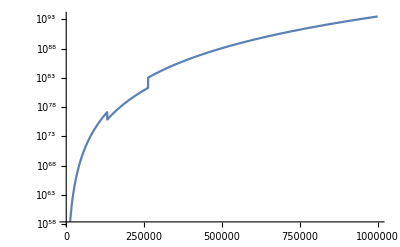

```mathematica
LogPlot[error[t],{t,0,escTime}]
```

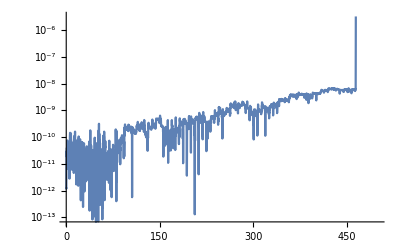

```mathematica
LogPlot[error[t],{t,0,500}]
```

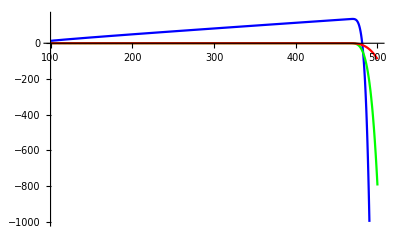

```mathematica
Plot[{ρ[σ]/.First@sol,ρ'[σ]/.First@sol,ρ''[σ]/.First@sol},{σ,100,500},PlotStyle->{Blue,Green,Red},PlotRange->{All,{-1000,150}}]
```

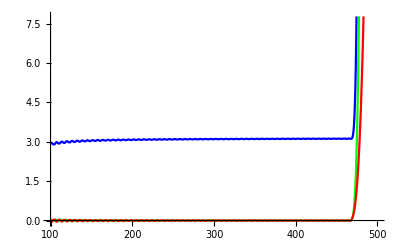

```mathematica
Plot[{θ[σ]/.First@sol,θ'[σ]/.First@sol,θ''[σ]/.First@sol},{σ,100,500},PlotStyle->{Blue,Green,Red}]
```

## With WorkingPrecision (with MaxSteps)

```mathematica
escTime=MaximumT+1;
initVelocities=getVelocities[b,1.2,-1];
sol=Quiet@NDSolve[{ddrho[0.5],ddθ[0.5],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->25,MaxSteps->∞];
```

```mathematica
escTime
```

3342.277334951729047617694

```mathematica
enSquaredNumerical[σ_]=(ρ'[σ]^2+ρ[σ](ρ[σ]-1)θ'[σ]^2+(1-1/ρ[σ])(1+((l[0.5]-0.5*ρ[σ]^2*Sin[θ[σ]]^2)^2)/(ρ[σ]^2 Sin[θ[σ]]^2)))/.First@sol;
```

```mathematica
error[σ_]=Abs[1.2^2-enSquaredNumerical[σ]];
```

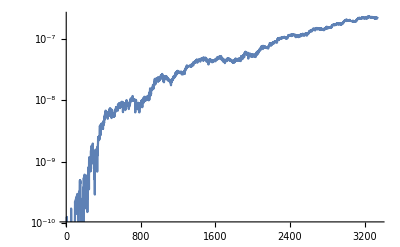

```mathematica
LogPlot[error[t],{t,0,escTime}]
```

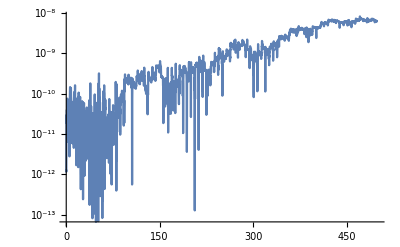

```mathematica
LogPlot[error[t],{t,0,500}]
```

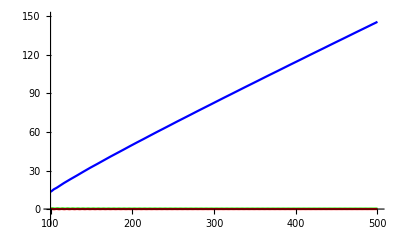

```mathematica
Plot[{ρ[σ]/.First@sol,ρ'[σ]/.First@sol,ρ''[σ]/.First@sol},{σ,100,500},PlotStyle->{Blue,Green,Red},PlotRange->{All,{-10,150}}]
```

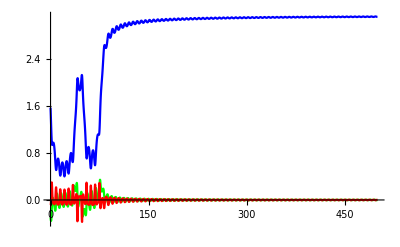

```mathematica
Plot[{θ[σ]/.First@sol,θ'[σ]/.First@sol,θ''[σ]/.First@sol},{σ,0,500},PlotStyle->{Blue,Green,Red}]
```

## Without WorkingPrecision

```mathematica
escTime=MaximumT+1;
initVelocities=getVelocities[b,1.2,-1];
sol=First@Quiet@NDSolve[{ddrho[0.5],ddθ[0.5],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1}];
```

```mathematica
escTime
```

3336.

```mathematica
enSquaredNumerical[σ_]=(ρ'[σ]^2+ρ[σ](ρ[σ]-1)θ'[σ]^2+(1-1/ρ[σ])(1+((l[0.5]-0.5*ρ[σ]^2*Sin[θ[σ]]^2)^2)/(ρ[σ]^2 Sin[θ[σ]]^2)))/.sol;
```

```mathematica
error[σ_]=Abs[1.2^2-enSquaredNumerical[σ]];
```

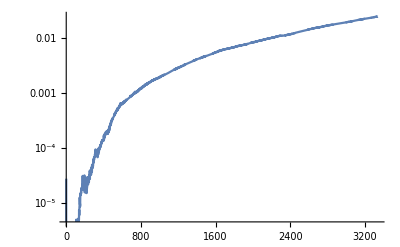

```mathematica
LogPlot[error[t],{t,0,escTime}]
```

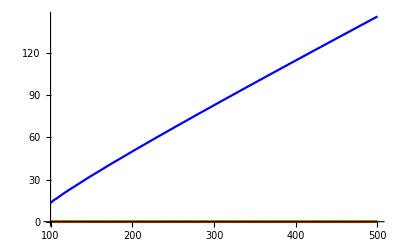

```mathematica
Plot[{ρ[σ]/.sol,ρ'[σ]/.sol,ρ''[σ]/.sol},{σ,100,500},PlotStyle->{Blue,Green,Red}]
```

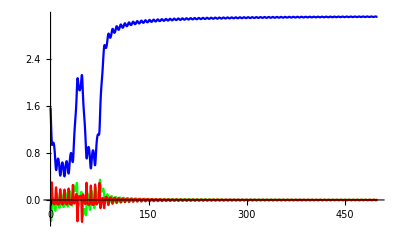

```mathematica
Plot[{θ[σ]/.sol,θ'[σ]/.sol,θ''[σ]/.sol},{σ,0,500},PlotStyle->{Blue,Green,Red}]
```